# 20 Gaussian Elimination: LU Decomposition

We know how to solve triangular systems of equations.  We are going to see how to reduce a general system 
	A.x=b 
to two triangular systems.

### Simple Matrices

What does the matrix below do?

```mathematica
L3=IdentityMatrix[8]; L3⟦4;;8,3⟧={L43,L53,L63,L73,L83};
MatrixForm[L3]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | L43 | 1 | 0 | 0 | 0 | 0
0 | 0 | L53 | 0 | 1 | 0 | 0 | 0
0 | 0 | L63 | 0 | 0 | 1 | 0 | 0
0 | 0 | L73 | 0 | 0 | 0 | 1 | 0
0 | 0 | L83 | 0 | 0 | 0 | 0 | 1)

Can you just write down its inverse?

```mathematica
MatrixForm[Inverse[L3]]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | -L43 | 1 | 0 | 0 | 0 | 0
0 | 0 | -L53 | 0 | 1 | 0 | 0 | 0
0 | 0 | -L63 | 0 | 0 | 1 | 0 | 0
0 | 0 | -L73 | 0 | 0 | 0 | 1 | 0
0 | 0 | -L83 | 0 | 0 | 0 | 0 | 1)

### Multiplying Simple Matrices

Here is another “similar” matrix

```mathematica
L4=IdentityMatrix[8]; L4⟦5;;8,4⟧={L54,L64,L74,L84};
MatrixForm[L4]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | L54 | 1 | 0 | 0 | 0
0 | 0 | 0 | L64 | 0 | 1 | 0 | 0
0 | 0 | 0 | L74 | 0 | 0 | 1 | 0
0 | 0 | 0 | L84 | 0 | 0 | 0 | 1)

The product L3.L4 is simple

```mathematica
MatrixForm[L3.L4]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | L43 | 1 | 0 | 0 | 0 | 0
0 | 0 | L53 | L54 | 1 | 0 | 0 | 0
0 | 0 | L63 | L64 | 0 | 1 | 0 | 0
0 | 0 | L73 | L74 | 0 | 0 | 1 | 0
0 | 0 | L83 | L84 | 0 | 0 | 0 | 1)

However, the product L4.L3 is not. To use these matrices we need to wrok down.

```mathematica
MatrixForm[L4.L3]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | L43 | 1 | 0 | 0 | 0 | 0
0 | 0 | L53+L43 L54 | L54 | 1 | 0 | 0 | 0
0 | 0 | L63+L43 L64 | L64 | 0 | 1 | 0 | 0
0 | 0 | L73+L43 L74 | L74 | 0 | 0 | 1 | 0
0 | 0 | L83+L43 L84 | L84 | 0 | 0 | 0 | 1)

### Chaining Simple Matrices

```mathematica
Clear[L]
MatrixForm[
Mat=LowerTriangularize[Table[StringForm["L````",i,j],{i,8},{j,8}],-1]+IdentityMatrix[8]
]
```

The lower triangular matrix below is the product of 7 of these simple matrices.

```mathematica
Clear[L]
MatrixForm[
Mat=LowerTriangularize[Table[StringForm["L````",i,j],{i,8},{j,8}],-1]+IdentityMatrix[8]
]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
L21 | 1 | 0 | 0 | 0 | 0 | 0 | 0
L31 | L32 | 1 | 0 | 0 | 0 | 0 | 0
L41 | L42 | L43 | 1 | 0 | 0 | 0 | 0
L51 | L52 | L53 | L54 | 1 | 0 | 0 | 0
L61 | L62 | L63 | L64 | L65 | 1 | 0 | 0
L71 | L72 | L73 | L74 | L75 | L76 | 1 | 0
L81 | L82 | L83 | L84 | L85 | L86 | L87 | 1)

## Using these Simple Matrices to Create Zeros

### Manually

Gaussian Elimination is the first way people worked out to make zeros. Note, if you were solving equations by candle light in 18XX you would not organize it this way!

```mathematica
m=8;
A0=RandomReal[{-1,1},{m,m}];
L1=IdentityMatrix[m]; L1⟦2;;m,1⟧=A0⟦2;;m,1⟧/A0⟦1,1⟧;
MatrixForm[A1 = Chop[Inverse[L1].A0]]
```

(-0.0568447 | -0.0966521 | 0.961492 | -0.678972 | -0.820617 | 0.294966 | -0.11328 | 0.476267
0 | -0.678703 | 14.3732 | -10.4522 | -12.7055 | 4.65333 | -1.47551 | 6.35576
0 | -0.507268 | 11.7288 | -9.09449 | -10.3222 | 4.48843 | -1.84444 | 6.30084
0 | 1.17852 | -13.3552 | 9.13145 | 10.9292 | -3.22584 | 0.959384 | -6.6363
0 | 0.539758 | -2.87721 | 1.99517 | 2.95525 | -0.551112 | -0.308468 | -2.50334
0 | 0.242384 | 3.34502 | -2.63357 | -3.8932 | 0.778041 | -1.12728 | 1.73105
0 | 1.26059 | -13.3639 | 10.2202 | 12.4315 | -4.96718 | 1.04803 | -7.67375
0 | 1.27371 | -7.10934 | 4.58514 | 6.52367 | -2.33329 | 1.24877 | -3.94063)

If we do it again we can make another almost column of zeros.

```mathematica
L2=IdentityMatrix[m]; L2⟦3;;m,2⟧=A1⟦3;;m,2⟧/A1⟦2,2⟧;
MatrixForm[A2 = Chop[Inverse[L2].A1]]
```

(-0.0568447 | -0.0966521 | 0.961492 | -0.678972 | -0.820617 | 0.294966 | -0.11328 | 0.476267
0 | -0.678703 | 14.3732 | -10.4522 | -12.7055 | 4.65333 | -1.47551 | 6.35576
0 | 0 | 0.986126 | -1.28244 | -0.82606 | 1.01049 | -0.741632 | 1.55049
0 | 0 | 11.603 | -9.01808 | -11.1331 | 4.85436 | -1.60275 | 4.40007
0 | 0 | 8.55351 | -6.31723 | -7.14914 | 3.14958 | -1.48191 | 2.55126
0 | 0 | 8.47811 | -6.36634 | -8.43069 | 2.43988 | -1.65423 | 4.00087
0 | 0 | 13.3322 | -9.19315 | -11.167 | 3.67568 | -1.69251 | 4.13113
0 | 0 | 19.8647 | -15.0304 | -17.3205 | 6.39957 | -1.52031 | 7.98717)

We can keep going.

```mathematica
L3=IdentityMatrix[m]; L3⟦4;;m,3⟧=A2⟦4;;m,3⟧/A2⟦3,3⟧;
MatrixForm[A3 = Chop[Inverse[L3].A2]]
L4=IdentityMatrix[m]; L4⟦5;;m,4⟧=A3⟦5;;m,4⟧/A3⟦4,4⟧;
MatrixForm[A4 = Chop[Inverse[L4].A3]]
L5=IdentityMatrix[m]; L5⟦6;;m,5⟧=A4⟦6;;m,5⟧/A4⟦5,5⟧;
MatrixForm[A5 = Chop[Inverse[L5].A4]]
L6=IdentityMatrix[m]; L6⟦7;;m,6⟧=A5⟦7;;m,6⟧/A5⟦6,6⟧;
MatrixForm[A6 = Chop[Inverse[L6].A5]]
L7=IdentityMatrix[m]; L7⟦8;;m,7⟧=A6⟦8;;m,7⟧/A6⟦7,7⟧;
MatrixForm[A7 = Chop[Inverse[L7].A6]]
```

(-0.0568447 | -0.0966521 | 0.961492 | -0.678972 | -0.820617 | 0.294966 | -0.11328 | 0.476267
0 | -0.678703 | 14.3732 | -10.4522 | -12.7055 | 4.65333 | -1.47551 | 6.35576
0 | 0 | 0.986126 | -1.28244 | -0.82606 | 1.01049 | -0.741632 | 1.55049
0 | 0 | 0 | 6.07144 | -1.41342 | -7.03528 | 7.12348 | -13.8433
0 | 0 | 0 | 4.80647 | 0.015985 | -5.61523 | 4.95089 | -10.8974
0 | 0 | 0 | 4.65931 | -1.32872 | -6.24768 | 4.72188 | -9.32927
0 | 0 | 0 | 8.14516 | 0.00115726 | -9.98588 | 8.33418 | -16.8311
0 | 0 | 0 | 10.8034 | -0.680204 | -13.9559 | 13.4193 | -23.2462)

(-0.0568447 | -0.0966521 | 0.961492 | -0.678972 | -0.820617 | 0.294966 | -0.11328 | 0.476267
0 | -0.678703 | 14.3732 | -10.4522 | -12.7055 | 4.65333 | -1.47551 | 6.35576
0 | 0 | 0.986126 | -1.28244 | -0.82606 | 1.01049 | -0.741632 | 1.55049
0 | 0 | 0 | 6.07144 | -1.41342 | -7.03528 | 7.12348 | -13.8433
0 | 0 | 0 | 0 | 1.13492 | -0.0457343 | -0.688427 | 0.0616883
0 | 0 | 0 | 0 | -0.24404 | -0.848706 | -0.744779 | 1.2943
0 | 0 | 0 | 0 | 1.89734 | -0.54767 | -1.22234 | 1.74048
0 | 0 | 0 | 0 | 1.83482 | -1.43746 | 0.743896 | 1.38642)

(-0.0568447 | -0.0966521 | 0.961492 | -0.678972 | -0.820617 | 0.294966 | -0.11328 | 0.476267
0 | -0.678703 | 14.3732 | -10.4522 | -12.7055 | 4.65333 | -1.47551 | 6.35576
0 | 0 | 0.986126 | -1.28244 | -0.82606 | 1.01049 | -0.741632 | 1.55049
0 | 0 | 0 | 6.07144 | -1.41342 | -7.03528 | 7.12348 | -13.8433
0 | 0 | 0 | 0 | 1.13492 | -0.0457343 | -0.688427 | 0.0616883
0 | 0 | 0 | 0 | 0 | -0.85854 | -0.89281 | 1.30757
0 | 0 | 0 | 0 | 0 | -0.471212 | -0.0714466 | 1.63735
0 | 0 | 0 | 0 | 0 | -1.36352 | 1.85687 | 1.28669)

(-0.0568447 | -0.0966521 | 0.961492 | -0.678972 | -0.820617 | 0.294966 | -0.11328 | 0.476267
0 | -0.678703 | 14.3732 | -10.4522 | -12.7055 | 4.65333 | -1.47551 | 6.35576
0 | 0 | 0.986126 | -1.28244 | -0.82606 | 1.01049 | -0.741632 | 1.55049
0 | 0 | 0 | 6.07144 | -1.41342 | -7.03528 | 7.12348 | -13.8433
0 | 0 | 0 | 0 | 1.13492 | -0.0457343 | -0.688427 | 0.0616883
0 | 0 | 0 | 0 | 0 | -0.85854 | -0.89281 | 1.30757
0 | 0 | 0 | 0 | 0 | 0 | 0.418575 | 0.919692
0 | 0 | 0 | 0 | 0 | 0 | 3.27481 | -0.789965)

(-0.0568447 | -0.0966521 | 0.961492 | -0.678972 | -0.820617 | 0.294966 | -0.11328 | 0.476267
0 | -0.678703 | 14.3732 | -10.4522 | -12.7055 | 4.65333 | -1.47551 | 6.35576
0 | 0 | 0.986126 | -1.28244 | -0.82606 | 1.01049 | -0.741632 | 1.55049
0 | 0 | 0 | 6.07144 | -1.41342 | -7.03528 | 7.12348 | -13.8433
0 | 0 | 0 | 0 | 1.13492 | -0.0457343 | -0.688427 | 0.0616883
0 | 0 | 0 | 0 | 0 | -0.85854 | -0.89281 | 1.30757
0 | 0 | 0 | 0 | 0 | 0 | 0.418575 | 0.919692
0 | 0 | 0 | 0 | 0 | 0 | 0 | -7.98538)

### Script

All this typing is nuts.  All the L entries can be stored in the same place.  We can recycle the storage for the matrix that winds up being U (the things called A0, A1, …) up above.  Finally, since only a few rows of the matrix are changed at a time changed at a time we might as well do only those rows

3.13704×10^-15

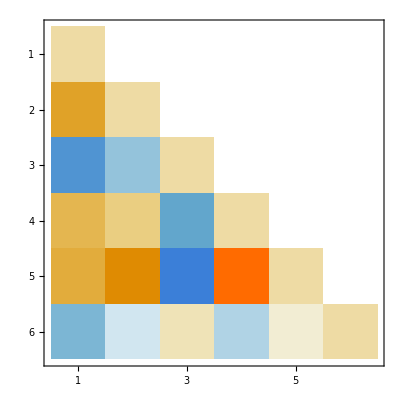
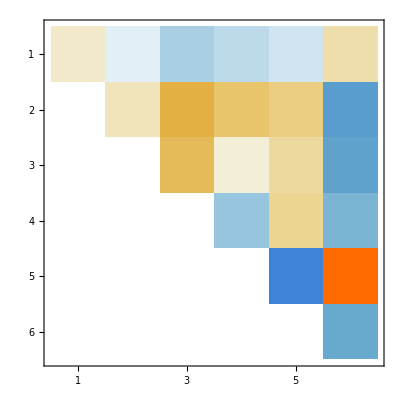

```mathematica
m=6;
A=RandomReal[{-1,1},{m,m}];
(* Start Script *)
L=IdentityMatrix[m];
U=A; 
Do[
Do[
L⟦j,k⟧=U⟦j,k⟧/U⟦k,k⟧;
U⟦j,k;;m⟧-=L⟦j,k⟧ U⟦k,k;;m⟧,
{j,k+1,m}],
{k,1,m-1}]
Norm[A-L.U]
Map[MatrixPlot,{L,U}]
```

### Function

2.13735×10^-14

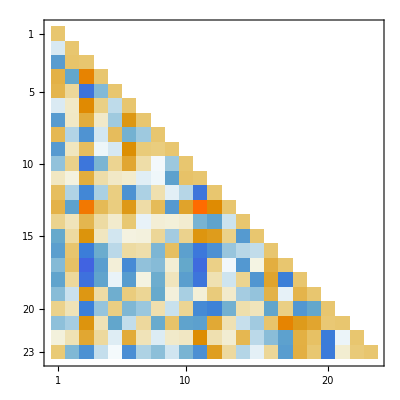
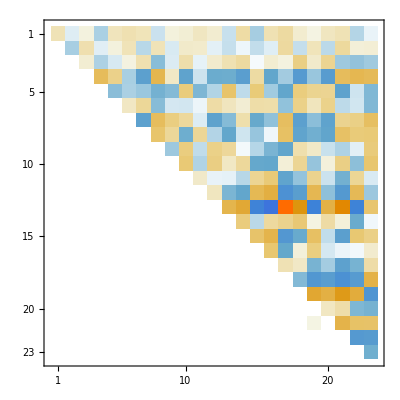

```mathematica
MyLUDecomposition[A_]:= Module[{m=Length[A],L,U=A},
(* Start Script *)
L=IdentityMatrix[m];
Do[
Do[
L⟦j,k⟧=U⟦j,k⟧/U⟦k,k⟧;
U⟦j,k;;m⟧-=L⟦j,k⟧ U⟦k,k;;m⟧,
{j,k+1,m}],
{k,1,m-1}];
{L,U}
]

m=23;
A=RandomReal[{-1,1},{m,m}];
{L,U}=MyLUDecomposition[A];
Norm[A-L.U]
Map[MatrixPlot,{L,U}]
```

## Solving a Linear System with an LU Decomposition

We know how to solve triangular systems. we even know that the obvious algorithm is backwards stable. We now know how to split a matrix up into two triangular matrices A=L.U.  we should be able to put this together to get an algorithm to solve A.x=L.U.x=b. All we need to do is make up an intermediate variable.  y=U.x 
	L.(U.x)=L.y=b
Solve L.y=b to get a ỹ.  Then solve U.x=ỹ to get x̃.  Since the triangular solves are backwards stable this would all be great if the L.U decomposition was stable!  It is not!

### Need for Pivoting

There are perfectly well behaved linear systems which will break our first attempt at an LU decomposition.  For example
	(ϵ | 1.0
1.0 | 1.0).(x1
x2)=(b1
b2).
In exact arithmetic Gaussian elimination gives the solution
	x1 | = | (b1-b2)/(-1+ϵ) | ⟶ | b2-b1
x2 | = | (-b1+b2 ϵ)/(-1+ϵ) | ⟶ | b1
The system is fine as ϵ→0.  Our first attempt at an LU decomposition gives. 
	A=(ϵ | 1.0
1.0 | 1.0)=(1 | 0
ϵ^-1 | 1)(ϵ | 1.0
0 | 1-ϵ^-1)
which in exact arithmetic works just fine: exact arithmetic does not care that ϵ^-1 could be huge. On any computer this is a real problem!  When ϵ is small in floating point the last entry gets messed up and we will get 
	 (1 | 0
ϵ^-1 | 1)(ϵ | 1.0
0 | -ϵ^-1)=(ϵ | 1
1 | 0)

The sad thing is this has nothing to do with the equations/matrix. As ϵ→0 the condition number κ(A) is the singular value ratio of ratio of (0 | 1.0
1.0 | 1.0) which is roughly 3.

The really sad thing is that if we had just written down the equations in a different order we would have got (1.0 | 1.0
ϵ | 1.0)=(1 | 0
ϵ | 1)(1 | 1
0 | 1-ϵ) which would have worked just fine.

We can not write a usage guide for a function that says “make sure your equations are in a decent order”. We need to make an algorithm that reorders the equations (rows in the matrix) into a good order on the fly.

The first question is given a matrix A which row (same as equation) should we start with.

After the first row we just ask which of the remaining rows is best to do next.

The resulting algorithm is called an LU decomposition with row pivoting.

You can also ask which remaining variable (column of the matrix would be best) which gives column pivoting.

If you ask which is the best variable and equation you are doing complete pivoting!